## Wechat Chat History Tools

Version 2:
Database format based on the newest version as of 2016 Dec
If you receive lots of errors, it is likely that the database format has changed again, since this has happened before.

User manual: evaluate all cells in the given order, change the information specified. You can ignore the comments in code.

### Initialization code

```mathematica
(*don't forget to evaluate this line, I will not set an initialization cell to confuse you*)
Needs["DatabaseLink`"];
```

Change the following paths to the two sqlite files according to README

```mathematica
mmPath="/Users/ywz/Desktop/desktop-old/App - com.tencent.xin/Documents/d3a6a48811066d9529906f3cee6cf8ca/DB/MM.sqlite";
contactPath="/Users/ywz/Desktop/desktop-old/App - com.tencent.xin/Documents/d3a6a48811066d9529906f3cee6cf8ca/DB/WCDB_Contact.sqlite";
mmConn=OpenSQLConnection[JDBC["SQLite",mmPath]];
contConn=OpenSQLConnection[JDBC["SQLite",contactPath]];
rawcontact=SQLSelect[contConn,"Friend"];
(*the function does not handle emoji in names because MMA does not support it*)
(*shortest pattern to match username, nickname, internalID, has issues, eats first letter of user defined ID occasionally*)readContact[{username_,SQLBinary[{Longest[x__]/;Length[{x}]>1,18,y__,26,z__,34,___}],profile_}]:={username,Sequence@@(FromCharacterCode[#,"UTF-8"]&/@{Drop[{x},2],Drop[{y},1],Drop[{z},1]}),profile[[1,2]]};
readContact[___]:=Nothing;
(*01 is male, 02 is female, 00 is unknown*)
contact=readContact/@rawcontact[[All,{1,8,10}]]//Quiet;
chatID="Chat_"<>IntegerString[Hash[#,"MD5"],16,32]&/@(Transpose[contact])[[1]];
getInfo=AssociationThread[chatID,contact];
availChatID=Select[SQLTableNames[mmConn],StringContainsQ[#,"Chat_"]&];
availUserInfo=Lookup[getInfo,availChatID];
chatData=(SQLSelect[mmConn,#]&/@availChatID)[[All,All,{4,5,9}]];
(*the time stamp is the second elapsed from 1970-1-1 8:00AM (GMT+8)*)
(*convert time to date string, for output*)
toDateString=DateString@AbsoluteTime[2209017600+#]&;
(*convert date string to internal time, for selection*)
toInternalTime=AbsoluteTime[#]-2209017600&;
(*since order is preserved, any other info than time is useless for counting, improves performance*)
(*but to analysis contents, use full database chatData instead*)
chatTimeStamps=chatData[[All,All,1]];
(*all message counts*)
topAllChats[anydb_]:=Transpose[{Length/@anydb,availUserInfo}]//Sort//Reverse;
(*note: be aware of the precedence of the Alternative operator in string patterns*)
topAllChatsNoGroup[anydb_]:=(Transpose[{Length/@anydb,availUserInfo}]//Sort//Reverse)/.{_,{_?(StringMatchQ[#,(__~~"@chatroom")|("gh_"~~__)]&),__}}:>Nothing;
(*performs counting over a specific time range*)
(*function takes two DateObjects*)
takeTimeStampRange[timestampdb_,start_,end_]:=With[{s=toInternalTime[start],e=toInternalTime[end]},Select[s≤#≤e&]/@timestampdb];
takeTimeRange[fulldb_,start_,end_]:=With[{s=toInternalTime[start],e=toInternalTime[end]},Select[s≤#[[1]]≤e&]/@fulldb];
(*generate a random time range*)
randomDateRange[timestampdb_]:=Module[{lowerlim,upperlim},{lowerlim,upperlim}=MinMax@Flatten@timestampdb;DateObject/@Sort@RandomInteger[{lowerlim,upperlim}+2209017600,2]];
(*get chat data for a specfic user by internalID*)
userChat[fulldb_,id_String]:=Position[availUserInfo,id]//Flatten//First//fulldb[[#]]&;
(*distribution of messages over time*)
toTimeSeries[singledb_,period:("Week"|"Month")]:=Module[{firstDay,lastDay,timedomain,counts},{firstDay,lastDay}=MinMax[Flatten@singledb[[All,1]]+2209017600];timedomain=DateRange[DateObject[firstDay],DateObject[lastDay], {1,period}];counts=BinLists[singledb[[All,1]],{AbsoluteTime/@timedomain-2209017600}]//Length/@#&;Transpose[{timedomain[[;;-2]],counts}]
];
(*unfortunately, excel format does not have that may rows to store all chats*)
(*Export["chat_history.xlsx",Thread[availUserInfo[[All,2]]->chatData]]*)
exportAllHistory[filename_]:=Export[filename,Join@@(Level[#,{-2}]&/@Transpose[{availUserInfo,MapAt[toDateString,chatData[[All,All,{1,3,2}]],{All,All,1}]}])]//AbsoluteTiming;
```

### All message counts

```mathematica
(*include groups and subscriptions, first 20*)
top20All=topAllChats[chatTimeStamps]//Take[#,UpTo[20]]&;
(*for privacy reasons, only message counts are displayed as a public example. But the variable top20All will contain all infomation in your run*)
top20All[[All,1]]
```

{69321,28993,27602,24325,19306,18702,16936,16725,15547,13466,13341,11191,10958,10687,10084,7974,7915,5885,5634,5459}

```mathematica
(*exclude groups and subscriptions, first 20*)
top20=topAllChatsNoGroup[chatTimeStamps]//Take[#,UpTo[20]]&;
(*message counts only*)
top20[[All,1]]
```

{24325,19306,16936,16725,13466,11191,10687,7974,5459,3915,3459,2468,2317,1983,1856,1556,1485,1214,1196,1173}

### Message counts over a certain time range

```mathematica
(*generate a random time interval*)
{date1,date2}=randomDateRange[chatTimeStamps];
```

```mathematica
(*in practice, you may want to specify a time range manually, here is how to do it*)
(*suppose you want the start date (date1 variable) to be 2016-08-17, you can do*)
date1=DateObject["2016-08-17"]
```

Wed 17 Aug 2016

```mathematica
partialChatTimeStamp=takeTimeStampRange[chatTimeStamps,date1,date2];
top20partial=topAllChatsNoGroup[partialChatTimeStamp]//Take[#,UpTo[20]]&;
(*message counts only*)
top20partial[[All,1]]
```

{9674,866,701,562,289,120,99,90,57,50,41,30,22,19,19,15,15,13,12,9}

### Analysis a single person

```mathematica
(*place the wechat id you want to analysis here, it is of form wxid_XXX..., you can get such information by evaluating `availUserInfo`*)
testid="wxid_XXXXXXXXXXXXXXX";
```

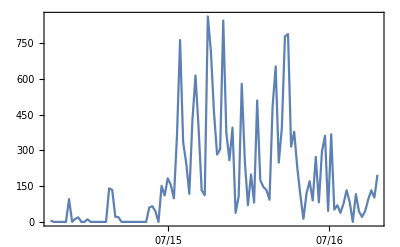

```mathematica
(*You can perform either a week or a month summation, by altering that "Week"/"Month"*)
(*in this picture, every datapoint(although they are connected) is a summation of week, the connection only shows the trend*)
DateListPlot[toTimeSeries[userChat[chatData,testid],"Week"],PlotRange->All,DateTicksFormat->{"Month", "/", "YearShort"}]
```

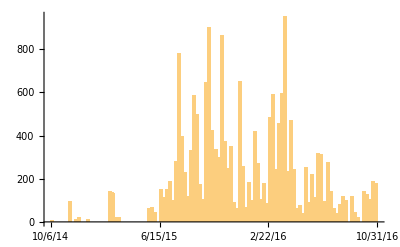

```mathematica
(*if you are not comfortable with the plot above, here is another option*)
DateHistogram[userChat[chatData,testid][[All,1]]+2209017600,"Week"]
```

### Export All Chat History as CSV

The file will be placed in your working directory if not specified.
Each line of chat data is of form: date string, sender(0 is yourself, 1 is the other, automatic specify person in groups), contents.
Different people/groups are separated by a line of user identity, it is of form: internal ID, name, user ID(if available), nickname(if available), gender.
Please note that exporting can take minutes if the database is large. And opening the CSV file with a professional text editor is strongly recommended, it can crash some editors that can’t handle big files.

```mathematica
exportAllHistory["history.csv"]
```

{106.129,history.csv}